### Supplementary code for simulations of D. suzukii population dynamics in “Large-scale open field trials in California and Oregon to evaluate the potential use of a new behavioral control system for Drosophila suzukii Matsumura (Diptera: Drosophilidae)” by Tait et al. (2022) Contact for code: ferdinand.pfab@gmail.com This file runs the simulations. Important: run weather_aurora.nb, parameter_fits_blueberry.nb, and insecticide_calculations.nb before.

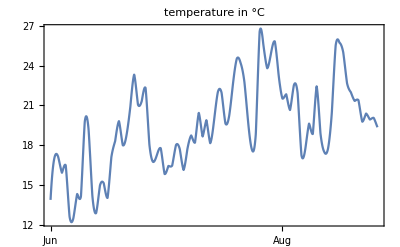

```mathematica
(*data from field trial*)
finalData={{"Treatment"->"GS","Date"->190,"Eggs"->0.0076923076900000005},{"Treatment"->"GS","Date"->193,"Eggs"->0.},{"Treatment"->"GS","Date"->195,"Eggs"->0.},{"Treatment"->"GS","Date"->198,"Eggs"->0.},{"Treatment"->"GS","Date"->200,"Eggs"->0.},{"Treatment"->"GS","Date"->202,"Eggs"->0.},{"Treatment"->"GS","Date"->204,"Eggs"->0.},{"Treatment"->"GS","Date"->206,"Eggs"->0.0076923076900000005},{"Treatment"->"GS","Date"->208,"Eggs"->0.},{"Treatment"->"GS","Date"->210,"Eggs"->0.},{"Treatment"->"GS","Date"->212,"Eggs"->0.},{"Treatment"->"GS","Date"->214,"Eggs"->0.},{"Treatment"->"GS","Date"->216,"Eggs"->0.},{"Treatment"->"GS","Date"->218,"Eggs"->0.},{"Treatment"->"GS","Date"->220,"Eggs"->0.},{"Treatment"->"GS","Date"->222,"Eggs"->0.},{"Treatment"->"GS","Date"->224,"Eggs"->0.},{"Treatment"->"GS","Date"->226,"Eggs"->0.},{"Treatment"->"GS","Date"->228,"Eggs"->0.},{"Treatment"->"GS","Date"->230,"Eggs"->0.},{"Treatment"->"GS","Date"->232,"Eggs"->0.},{"Treatment"->"GS","Date"->234,"Eggs"->0.},{"Treatment"->"GS","Date"->236,"Eggs"->0.0076923076900000005},{"Treatment"->"GUM","Date"->190,"Eggs"->0.},{"Treatment"->"GUM","Date"->193,"Eggs"->0.},{"Treatment"->"GUM","Date"->195,"Eggs"->0.},{"Treatment"->"GUM","Date"->198,"Eggs"->0.},{"Treatment"->"GUM","Date"->200,"Eggs"->0.},{"Treatment"->"GUM","Date"->202,"Eggs"->0.},{"Treatment"->"GUM","Date"->204,"Eggs"->0.008333333330000001},{"Treatment"->"GUM","Date"->206,"Eggs"->0.},{"Treatment"->"GUM","Date"->208,"Eggs"->0.},{"Treatment"->"GUM","Date"->210,"Eggs"->0.},{"Treatment"->"GUM","Date"->212,"Eggs"->0.},{"Treatment"->"GUM","Date"->214,"Eggs"->0.025},{"Treatment"->"GUM","Date"->216,"Eggs"->0.},{"Treatment"->"GUM","Date"->218,"Eggs"->0.},{"Treatment"->"GUM","Date"->220,"Eggs"->0.},{"Treatment"->"GUM","Date"->222,"Eggs"->0.008333333330000001},{"Treatment"->"GUM","Date"->224,"Eggs"->0.},{"Treatment"->"GUM","Date"->226,"Eggs"->0.},{"Treatment"->"GUM","Date"->228,"Eggs"->0.},{"Treatment"->"GUM","Date"->230,"Eggs"->0.},{"Treatment"->"GUM","Date"->232,"Eggs"->0.},{"Treatment"->"GUM","Date"->234,"Eggs"->0.},{"Treatment"->"GUM","Date"->236,"Eggs"->0.0416666667},{"Treatment"->"UTC","Date"->190,"Eggs"->0.0181818182},{"Treatment"->"UTC","Date"->193,"Eggs"->0.},{"Treatment"->"UTC","Date"->195,"Eggs"->0.},{"Treatment"->"UTC","Date"->198,"Eggs"->0.},{"Treatment"->"UTC","Date"->200,"Eggs"->0.},{"Treatment"->"UTC","Date"->202,"Eggs"->0.0181818182},{"Treatment"->"UTC","Date"->204,"Eggs"->0.},{"Treatment"->"UTC","Date"->206,"Eggs"->0.00909090909},{"Treatment"->"UTC","Date"->208,"Eggs"->0.00909090909},{"Treatment"->"UTC","Date"->210,"Eggs"->0.},{"Treatment"->"UTC","Date"->212,"Eggs"->0.},{"Treatment"->"UTC","Date"->214,"Eggs"->0.},{"Treatment"->"UTC","Date"->216,"Eggs"->0.},{"Treatment"->"UTC","Date"->218,"Eggs"->0.},{"Treatment"->"UTC","Date"->220,"Eggs"->0.},{"Treatment"->"UTC","Date"->222,"Eggs"->0.},{"Treatment"->"UTC","Date"->224,"Eggs"->0.},{"Treatment"->"UTC","Date"->226,"Eggs"->0.},{"Treatment"->"UTC","Date"->228,"Eggs"->0.00909090909},{"Treatment"->"UTC","Date"->230,"Eggs"->0.0363636364},{"Treatment"->"UTC","Date"->232,"Eggs"->0.},{"Treatment"->"UTC","Date"->234,"Eggs"->0.00909090909},{"Treatment"->"UTC","Date"->236,"Eggs"->0.290909091}};
(*the different treatments*)
treatments=Union["Treatment"/.finalData];
(*function to select data by key and value (used later to group by treatment)*)
SelectFromDataset[dataset_,key_,value_]:=Select[dataset,(key/.#)==value&];

(*output directory for plots*)
directory=NotebookDirectory[];
(*parameters*)
(*sex ratio*)
Πs=1/2;
(*fecundity of females*)
β[c_]:= gauss[c]/.fitfecundity;
(*mortality of juvenile stages*)
δv[c_]:= gaussinv[c]/.fitjmort;
(*mortality of egg stage*)
δe[c_]:=δv[c];
(*mortality of larval stage*)
δl[c_]:=δv[c];
(*mortality of pupal stage*)
δp[c_]:=δv[c];
(*number of substages of egg, larval, pupal and adult stages*)
ke=15;kl=25;kp=25;ka=4;

(*maturation speeds of egg, larvae, pupae and adults. Note: adult "maturation" means they die*)
ge[c_]:=ke/gaussinv[c]/.fitetol;
gl[c_]:=ke/gaussinv[c]/.fitltop;
gp[c_]:=kp/gaussinv[c]/.fitptoa;
ga[c_]:=ka/gauss[c]/.fitatom;
(*state variables: egg, larvae, pupae and adults. These are all vectors by themselves, including the substages*)
vars={e,l,p,a};
(*matrices for transitions between stages and substages*)
(*maturation between substages*)
mM[k_]:=SparseArray[Band[{2,1},{k,k-1},{1,1}]->1,{k,k}]-SparseArray[Band[{1,1},{k,k},{1,1}]->1,{k,k}];
(*maturation between stages*)
mS[k1_,k2_]:=SparseArray[{1,k2}->1,{k1,k2}];
(*fecundity: adults create new individuals in first egg substage*)
mF[k1_,k2_]:=SparseArray[Band[{1,1},{1,k2},{0,1}]->1,{k1,k2}];
(*vector to sum up all substages of a stage*)
vC[k_]:=Table[1,k];
(*start time of simulation*)
tmin=1;
(*start time of interventions*)
tintervention=39;
(*end time of simulation*)
tmax=87(*87*)(*110*);
(*function to run simulations*)
(*interventions = pesticide interventions, as defined below*)
(*fecundity is multiplied by βfactor, this is used to reduce the fecundity in the gum treatments (as eggs laid in gum do not develope)*)
Plot[w[t],{t,tmin,tmax},Frame->True,FrameTicks->{{Automatic,None},{xlabelsmonth,
None}},PlotLabel->"temperature in °C"(*(*,AxesOrigin->{Automatic,0}*)*)]
```

```mathematica
(*initial number of individuals*)
a0=.005;
(*
function to run simulation
a0: initial number of adults
βfactor: reduce fecundity by this factor (for GUM treatment)
μ's: pesticide induced mortality rates
tmin, tmax: time span of simulation
tintervention: start time of GUM and pesticide treatments
*)

sim[a0_,βfactor_,{μe_,μl_,μp_,μa_},tmin_,tmax_,tintervention_]:=
Module[{eqs,inis,γ,pesticidemortalityTIME,βfactorTIME},
(*make pesticide and GUM start at time tinervention*)
pesticidemortalityTIME=Piecewise[{{0, t<tintervention}, {1, True}}];

βfactorTIME=Piecewise[{{1, t<tintervention}, {βfactor, True}}];
(*this is the fecundity at time t, taken into account the sex rartio*)
γ[t_]:=Πs βfactorTIME β[w[t]];
(*differential equations, note that the state variables are vectors with the substages*)
eqs=
{
e'[t]==γ[t] mF[ke,ka].a[t]+ge[w[t]] mM[ke].e[t]-(δe[w[t]]+pesticidemortalityTIME μe)e[t],
l'[t]==ge[w[t]] mS[kl,ke].e[t]+gl[w[t]] mM[kl].l[t]-(δl[w[t]]+pesticidemortalityTIME μl) l[t],
p'[t]==gl[w[t]] mS[kp,kl].l[t]+gp[w[t]] mM[kp].p[t]-(δp[w[t]]+pesticidemortalityTIME μp) p[t],
a'[t]==gp[w[t]] mS[ka,kp].p[t]+ga[w[t]] mM[ka].a[t]-pesticidemortalityTIME μa a[t]
};
(*initial conditions, start with only adults. Those adults are distributed uniformly over the adult substages*)
inis={
e[tmin]==Table[0,ke],
l[tmin]==Table[0,kl],
p[tmin]==Table[0,kp],
a[tmin]==Table[a0/ka,ka]
};
(*solve the ODEs numerically*)
NDSolve[
Flatten[{
eqs,
inis
}],
vars,
{t,tmin,tmax}
]];
(*some style*)
font="Times New Roman";
thickness=Thickness[.008];
style={PlotStyle->thickness,LabelStyle->{FontFamily->font,20},
Frame->{{True,True},{True,True}},
ImagePadding->{{80,20},{30,15}},
PlotRangePadding->0,
ImageSize->500, 
FrameTicks->{{Automatic,None},{xlabelsmonth,
None}}};
colors=ColorData[97]&{3,2,1};
RColors=RGBColor@@#&/@(1/256{{240,228,66},{213,94,0},{0,114,178}});
(*shift time so that simulations are started at June 1*)
tshift=Total@monthlength[[1;;5]];
(*show simulatoins only after intializiation for 30 days - end of June*)
tminplot=30;
(*gum efficiency from Tait et al 2018, reduction of eggs in fruit close by (solid) gum*)
gumefficiency=14/28.7;
(*pesticide induced mortalities: egg, larvae, pupae and adults*)
(*the no-pesticide treatment*)
μ0={0,0,0,0};
(*the pesticide treatment*)
μ={e,l,p,a}/.finalMortalities;
```

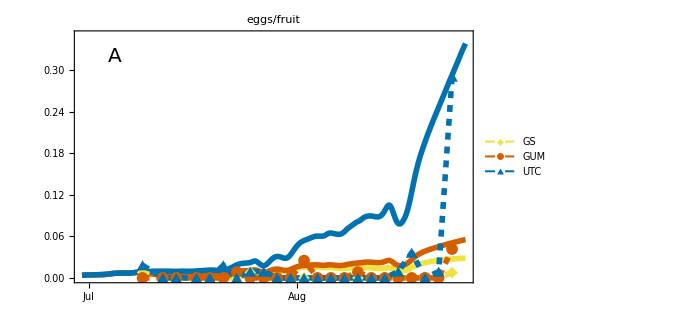

```mathematica
(*run simulations*)
With[{
(*the three different treatments in the field experiemnts: pesticide, GUM, no intervention*)
sols={

sim[a0,1,μ,tmin,tmax,tintervention],
sim[a0,gumefficiency,μ0,tmin,tmax,tintervention],
sim[a0,1,μ0,tmin,tmax,tintervention]}
},
(*show simulations and field data together*)
plotA=Show[{
Plot[Evaluate[vC[ke].e[t]/.#[[1]]&/@sols],{t,tminplot,tmax},PlotStyle->({thickness,#}&/@RColors),Evaluate@style,PlotLabel->"eggs/fruit",PlotRange->{0,.35},
Epilog->Inset[Style["A",20],Scaled[{.1,.9}]]
],
ListPlot[Table[{"Date"-tshift,"Eggs"}/.SelectFromDataset[finalData,"Treatment",treatment],{treatment,treatments}],PlotStyle->({thickness,Dashed,#}&/@RColors),Evaluate@style,Joined->True,PlotRange->Full,PlotLegends->(Style[#,16]&/@treatments),PlotMarkers->({Charting`CommonDump`GraphicsPlotMarkers[][[#,1]],12}&/@{3,1,4})]
}]
]
```

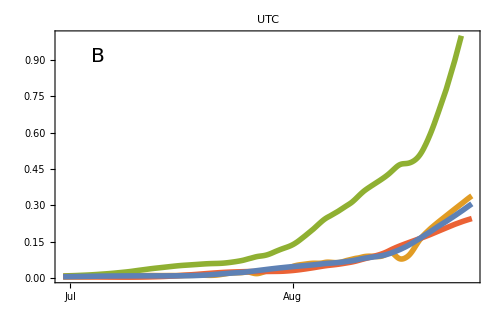
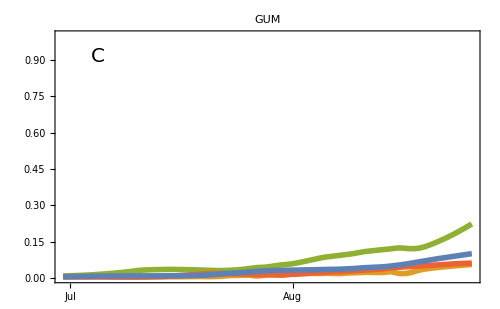
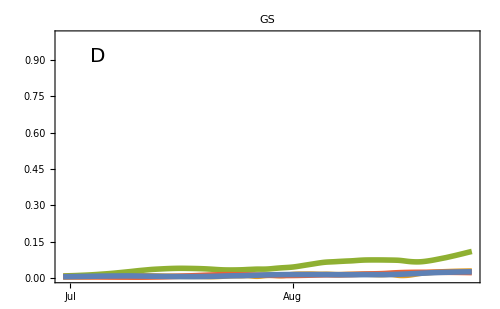
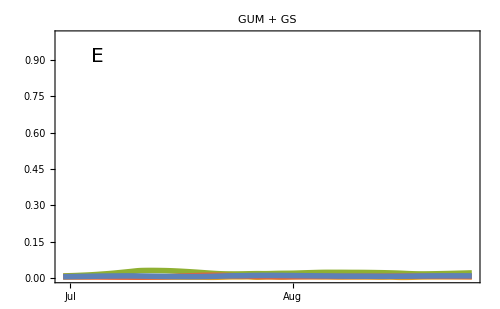
-Graphics- | -Graphics- |   eggs
-Graphics- |   larvae
-Graphics- |   pupae
-Graphics- |   adults | -Graphics- | -Graphics- |   eggs
-Graphics- |   larvae
-Graphics- |   pupae
-Graphics- |   adults
-Graphics- | -Graphics- |   eggs
-Graphics- |   larvae
-Graphics- |   pupae
-Graphics- |   adults | -Graphics- | -Graphics- |   eggs
-Graphics- |   larvae
-Graphics- |   pupae
-Graphics- |   adults

```mathematica
(*colors for different stages*)
colorselpa=ColorData[97]/@{2,3,4,1};
(*legend for additional simulations (stage strucured plots)*)
legend=Grid[Transpose[{Plot[.5,{x,0,1},PlotStyle->{#,Thickness[.1]},Axes->None,PlotRange->{0,1},ImageSize->25]&/@colorselpa,Style["  "<>#,16,FontFamily->font]&/@{"eggs","larvae","pupae","adults"}}],Alignment->Left];
(*function to plot the simulations (stage structured plots)*)
mkplot[pestidicide_,βfactor_,min_,max_,title_,tmin_,tmax_,tminplot_,inset_]:=
Module[{sol
},
sol=sim[a0,βfactor,pestidicide μ,tmin,tmax,tintervention];
Grid[{{
Plot[Evaluate[Flatten[{Table[vC[{ke,kl,kp,ka}[[i]]].({e,l,p,a}[[i]][t]/.sol[[1]]),{i,4}]
}]],{t,tminplot,tmax},PlotRange->{Automatic,{min,max}},
PlotLabel->title,
PlotStyle->Table[{col,Thickness[.008]},{col,colorselpa}],LabelStyle->{FontFamily->font,20},
Frame->{{True,True},{True,True}},
ImagePadding->{{80,20},{30,15}},
PlotRangePadding->0,
ImageSize->500, 
FrameTicks->{{Automatic,None},{xlabelsmonth,
None}},
Epilog->Inset[Style[inset,20],Scaled[{.1,.9}]]
],
legend
}},Alignment->Left]
];
plotBCD=Grid[{{
mkplot[0,1,0,1,"UTC",tmin,tmax,tminplot,"B"],

mkplot[0,gumefficiency,0,1,"GUM",tmin,tmax,tminplot,"C"]},
{
mkplot[1,1,0,1,"GS",tmin,tmax,tminplot,"D"],
mkplot[1,gumefficiency,0,1,"GUM + GS",tmin,tmax,tminplot,"E"]}
}]
```

```mathematica
(*export plots*)
(Export[directory<>"simulations.pdf",#];#)&@Column[{plotA,plotBCD},Alignment->Center]
```

-Graphics-
-Graphics- | -Graphics- |   eggs
-Graphics- |   larvae
-Graphics- |   pupae
-Graphics- |   adults | -Graphics- | -Graphics- |   eggs
-Graphics- |   larvae
-Graphics- |   pupae
-Graphics- |   adults
-Graphics- | -Graphics- |   eggs
-Graphics- |   larvae
-Graphics- |   pupae
-Graphics- |   adults | -Graphics- | -Graphics- |   eggs
-Graphics- |   larvae
-Graphics- |   pupae
-Graphics- |   adults